## Метод на допирателните (Нютон) за решаване на уравнения f(x) = 0

Задача: Дадено е уравнението 
(x^3+45 cos x-2)/((x-2)(x+3))+tg2x = 0.
a) Да се намери броят на всички корени и да се локализира този, който е най-близо до нулата.
б) Направете 2 итерации по метода на Нютон (допирателните).
в) Каква е точността на последно полученото в б) приближение? 
г) Да се намери локализирания от подточка а) корен с точност 10^-14.
д) Да се направи сравнение между метода на Нютон за поставената задача и метода на хордите и метода на разполовяването.

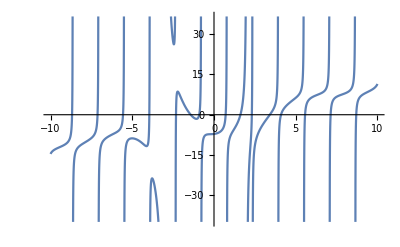

```mathematica
f[x_]:=(x^3+45 Cos[x]-2)/((x-2)(x+3))+Tan[2x]
Plot[f[x],{x,-10,10}]
```

ДС: (x-2)(x+3) ≠ 0, cos 2x ≠ 0
Извод: Функцията има безброй много корени.

### I. Локализация на корен: a = ?, b = ? , такива че x* ∈ [a, b]

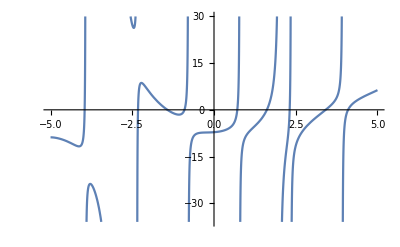

```mathematica
Plot[f[x],{x,-5,5}]
```

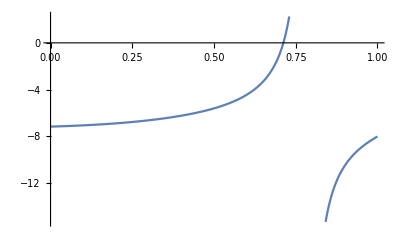

```mathematica
Plot[f[x],{x,0,1}]
```

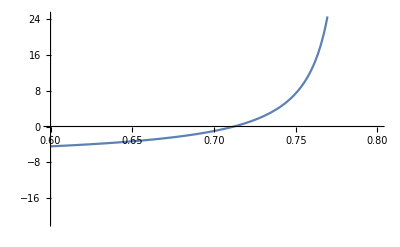

```mathematica
Plot[f[x],{x,0.6,0.8}]
```

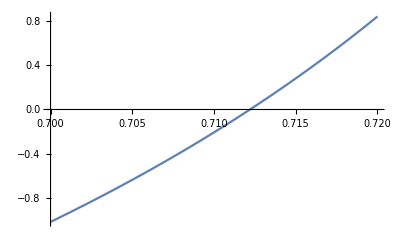

```mathematica
Plot[f[x],{x,0.7,0.72}]
```

### II. Проверка на условията за сходимост на метода: f’(x), f’’(x) да са с постоянни знаци в интервала [a, b]

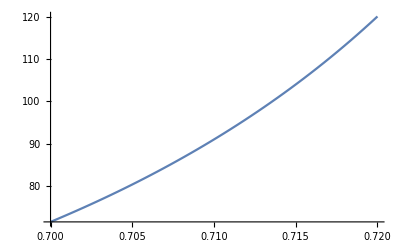

```mathematica
Plot[f'[x],{x,0.7,0.72}]
```

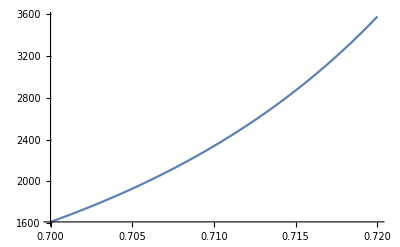

```mathematica
Plot[f''[x],{x,0.7,0.72}]
```

### III. Определяне на начално приближение: x_0 = ?, такова че f(x_0).f’’(x) > 0

f’’(x) > 0 за избрания интервал => f(x_0) >0

```mathematica
f[0.7]
```

-1.01311

```mathematica
f[0.72]
```

0.838447

```mathematica
x0 = 0.72
```

0.72

### IV. Уточняване на корена: x_(n+1) = x_n - (f(x_n))/(f'(x_n)), n = 0,1,2,... с оценка на грешката ϵ_n = |x* - x_n|: ϵ_n ⩽ M_2/(2 m_1) |x_n-x_(n-1)|^2, където M_2 = max_[a,b] |f’’(x)| , m_1 = min_[a,b] |f’(x)|

#### Определяне на постоянните величини M_2 = ?, m_1=?

```mathematica
Plot[Abs[f''[x]],{x,0.7,0.72}]
```

-Graphics-

```mathematica
M2 = Abs[f''[0.72]]
```

3581.01

```mathematica
Plot[Abs[f'[x]],{x,0.7,0.72}]
```

-Graphics-

```mathematica
m1= Abs[f'[0.7]]
```

71.5539

```mathematica
P = M2/(2 m1)
```

25.0232

#### Извършване на итерациите

Съставяме програмен код на Mathematica, който извършва итерациите и печата необходимите ни величини:

```mathematica
f[x_]:=(x^3+45 Cos[x]-2)/((x-2)(x+3))+Tan[2x]
x0 = 0.72;
M2 = Abs[f''[0.72]];
m1= Abs[f'[0.7]];
P = M2/(2 m1);
Print["n = ", 0, " x_n = ", x0, " f(x_n) = ", f[x0], " f'(x_n) = ", f'[x0]]
For[n=1,n<=2, n++,
x1 = x0 -f[x0]/f'[x0];
eps = P*Abs[x1-x0]^2;
x0 = x1;
Print["n = ", n, " x_n = ", x0, " f(x_n) = ", f[x0], " f'(x_n) = ", f'[x0], " ε_n = ", eps]
]
```

n = 0 x_n = 0.72 f(x_n) = 0.838447 f'(x_n) = 120.015

n = 1 x_n = 0.713014 f(x_n) = 0.0789681 f'(x_n) = 98.4969 ε_n = 0.00122131

n = 2 x_n = 0.712212 f(x_n) = 0.000839976 f'(x_n) = 96.4129 ε_n = 0.0000160843

повече итерации

```mathematica
f[x_]:=(x^3+45 Cos[x]-2)/((x-2)(x+3))+Tan[2x]
x0 = 0.72;
M2 = Abs[f''[0.72]];
m1= Abs[f'[0.7]];
P = M2/(2 m1);
Print["n = ", 0, " x_n = ", x0, " f(x_n) = ", f[x0], " f'(x_n) = ", f'[x0]]
For[n=1,n<=10, n++,
x1 = x0 -f[x0]/f'[x0];
eps = P*Abs[x1-x0]^2;
x0 = x1;
Print["n = ", n, " x_n = ", x0, " f(x_n) = ", f[x0], " f'(x_n) = ", f'[x0], " ε_n = ", eps]
]
```

n = 0 x_n = 0.72 f(x_n) = 0.838447 f'(x_n) = 120.015

n = 1 x_n = 0.713014 f(x_n) = 0.0789681 f'(x_n) = 98.4969 ε_n = 0.00122131

n = 2 x_n = 0.712212 f(x_n) = 0.000839976 f'(x_n) = 96.4129 ε_n = 0.0000160843

n = 3 x_n = 0.712203 f(x_n) = 9.70224×10^-8 f'(x_n) = 96.3907 ε_n = 1.89935×10^-9

n = 4 x_n = 0.712203 f(x_n) = 8.88178×10^-16 f'(x_n) = 96.3907 ε_n = 2.53523×10^-17

n = 5 x_n = 0.712203 f(x_n) = 8.88178×10^-16 f'(x_n) = 96.3907 ε_n = 0.

n = 6 x_n = 0.712203 f(x_n) = 8.88178×10^-16 f'(x_n) = 96.3907 ε_n = 0.

n = 7 x_n = 0.712203 f(x_n) = 8.88178×10^-16 f'(x_n) = 96.3907 ε_n = 0.

n = 8 x_n = 0.712203 f(x_n) = 8.88178×10^-16 f'(x_n) = 96.3907 ε_n = 0.

n = 9 x_n = 0.712203 f(x_n) = 8.88178×10^-16 f'(x_n) = 96.3907 ε_n = 0.

n = 10 x_n = 0.712203 f(x_n) = 8.88178×10^-16 f'(x_n) = 96.3907 ε_n = 0.

```mathematica
Precision[eps]
```

MachinePrecision

```mathematica
%//N
```

15.9546

### 💡 Тайни козове

#### Solve

#### FindRoot